```mathematica
coeff[x_,X_]:=Module[{len},
len=Length[X];
Table[Product[If[i==k,1,x-X[[k]]],{k,len}]/Product[If[i==j,1,X[[i]]-X[[j]]],{j,len}],{i,len}]
];
```

-34.9232

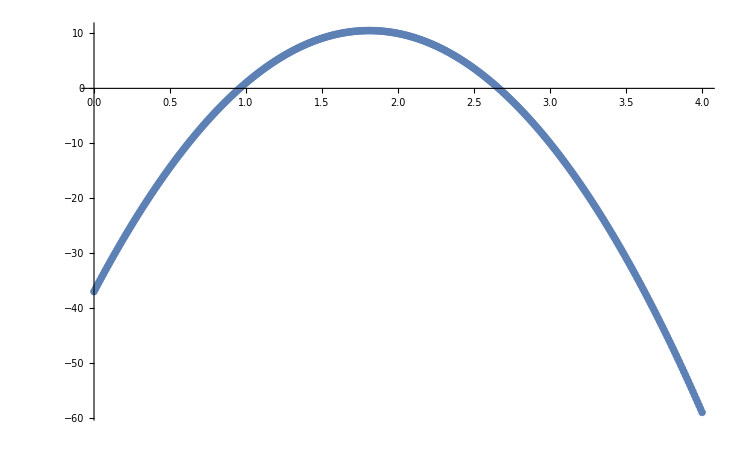

```mathematica
F[x_]:=Dot[coeff[x,{1,2,3}],{1,10,-10}]
tab =Table[{x,F[x]},{x,0,4,0.01}];
F[0.04]
ListPlot[tab]
```